## 一道极限问题

```mathematica
Limit[n ∫_0^π (x Sin[π^2/x] Sin[n x])ⅆx,n->+∞]
```

$Aborted

```mathematica
Table[n NIntegrate[x Sin[π^2/x]Sin[n x],{x,0,π}],{n,1,10}]
```

{-1.19213,3.53577,-2.75913,-2.11105,2.46061,2.62523,-0.72966,-2.89343,-1.80832,0.896768}

```mathematica
n=80075000;
n NIntegrate[x Sin[π^2/x]Sin[n x],{x,0,π},MaxRecursion->500,PrecisionGoal->12]
n=.
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.53194×10^-10 and 1.29089×10^-21 for the integral and error estimates.

0.044297

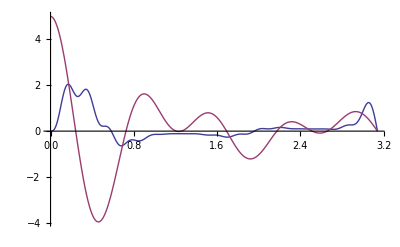

```mathematica
k=5;
Plot[{∑_(i=1)^12 (∑_(j=1)^k (Sin[(2i+j)x]/(2i+j)-Sin[(2i+k+j)x]/(2i+k+j))),Sin[(k x)/2]/Sin[x/2](Cos[(2k+3)/2 x])},{x,0,π},PlotRange->Full]
k=.
```

```mathematica
∑_(i=1)^∞ (Sin[i x]/(i+1))
```

-1/2 ⅈ ⅇ^(-ⅈ x) (-Log[1-ⅇ^(ⅈ x)]+ⅇ^(2 ⅈ x) Log[ⅇ^(-ⅈ x) (-1+ⅇ^(ⅈ x))])